```mathematica
<<Vilcretas`
```

VilCretas está disponible.

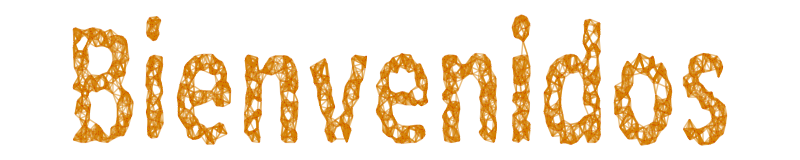

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
f = Sum[-13 i^3-14^(-7i)+7^(10i),{i, 2, n-1}];
g = {7^(10n),n*7^(10n),n^9,n^8,n^7,n^6,n^5,n^4,n^3,n^2,n,1};
Table[i->Limit[f/i,n->Infinity],{i,g}]
```

{7^(10 n)→1/282475248,7^(10 n) n→0,n^9→∞,n^8→∞,n^7→∞,n^6→∞,n^5→∞,n^4→∞,n^3→∞,n^2→∞,n→∞,1→∞}

```mathematica
Limit[f/7^(10n),n->Infinity]
```

1/282475248

```mathematica
Limit[1/7^(10 n)Sum[-13 i^3-14^(-7i)+7^(10i),{i, 2, n-1}], n->Infinity]
```

1/282475248

```mathematica
Table[i,{i,1,50,10}]
```

{1,11,21,31,41}

```mathematica
Clear[f,g]
```

```mathematica
f=Product[2^i/(16 i^2),{i,2, n-1}];

g=(2^(n^2))/(n!);
Limit[f/g, n->Infinity]
```

0

```mathematica
Limit[Sum[1,{i, 1,n^3+2}]/n^3,n->Infinity]
```

1

```mathematica
g={n^2,n^3,n^5,n^6,n^4};
Table[i->Limit[1/i Sum[Sum[1, {j,1,i+6}],{i, 1,n^3+2}],n->Infinity],{i,g}]
```

{n^2→∞,n^3→∞,n^5→∞,n^6→1/2,n^4→∞}